# Kawahara Stability Notebook

The first section of the notebook computes an elliptic standing wave solution to the Kawahara equation with a non-zero third order dispersion, and checks that it satisfies the the correct equation.

The Kawahara equation is 

u_t+ u u_x+ α u_xxx- u_xxxxx=0

By Galilean invariance it is sufficient to look for standing waves.

```mathematica
σ = 1/4
α =-2.0
KPoly= -703040 (m-2)(m+1)(2m-1) + 56784 s (m^2-m+1) - 31 s^3
```

1/4

-2.

-703040 (-2+m) (1+m) (-1+2 m)+56784 (1-m+m^2) s-31 s^3

```mathematica
mRoots=N[Solve[(KPoly /. s->α/(σ^2))==0,m],40]
```

{{m→-1.81177},{m→0.618488},{m→1.40097}}

```mathematica
mmm = (m /. mRoots[[2]])
```

0.618488

```mathematica
B3 = 1680 σ^4 mmm^2
B2 = -280/13 σ^2 mmm (-α + 104 σ^2 mmm - 52 σ^2)
B1 = (-31 α^2 + 264992 σ^4 mmm^2 - 264992 σ^4 mmm - 18928 σ^4 + 3640 α σ^2 - 7280 α σ^2 mmm)/(507)
Period = 2 EllipticK[mmm]/σ
```

2.51034

-2.30639

-0.659492

15.7605

```mathematica
ϕ[x_] := B1 + B2 JacobiCN[σ x,mmm]^2 + B3 JacobiCN[σ x , mmm]^4
```

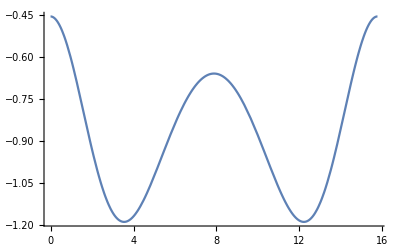

```mathematica
Plot[ϕ[x],{x,0,2 EllipticK[mmm]/σ}]
```

```mathematica
Err=Expand[ϕ[x]D[ϕ[x],x] + α D[ϕ[x],{x,3}] - D[ϕ[x],{x,5}]];
```

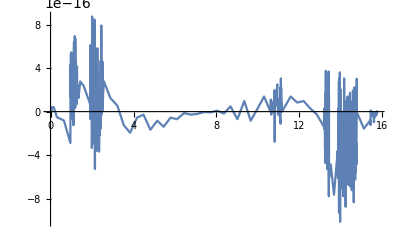

```mathematica
Plot[Err,{x,0,2 EllipticK[mmm]/σ},PlotRange->All]
```

Err should be zero if ϕ[x] solves the Kawahara traveling wave equation, so everything looks good.

```mathematica
KI = EllipticK[mmm]
EI= EllipticE[mmm]
KP = EllipticK[1-mmm]
qn = Exp[- Pi KP/KI]
```

1.97006

1.28832

1.76491

0.0599378

These are the analytical expressions for the Fourier coefficients of cn^2 and cn^4. These were worked out using the ideas in Kiper’s paper. We have expressions for both the cn^2 and cn^4 terms in the solution.

```mathematica
AF2[k_] :=Pi^2/( KI^2 mmm)  k qn^k/(1-qn^(2k))
A02 = (EI - KI (1-mmm))/(KI mmm)
AF4[k_] :=  Pi^2/(6 KI^2 mmm^2) (Pi^2 k^3/(KI^2) - 4 (1-2mmm) k) qn^k/(1-qn^(2k))
A04 = -2(1-2 mmm)/(3mmm) ((EI - KI (1-mmm))/(KI mmm))+ (1-mmm)/(3 mmm)
```

0.440488

0.318132

```mathematica
FS2 = A02+ 2Sum[AF2[k] Cos[k Pi x/KI],{k,1,nmodes}];
FS4 = A04 +2 Sum[AF4[k] Cos[k Pi x/KI],{k,1,nmodes}];
```

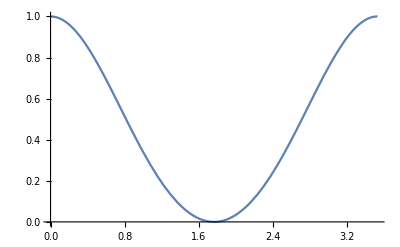

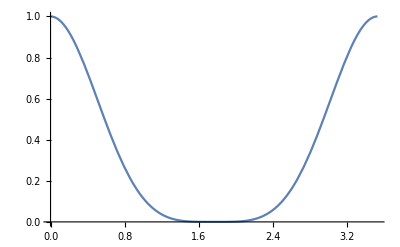

```mathematica
Plot[FS2,{x,0,Period/4}]
Plot[FS4,{x,0,Period/4}]
```

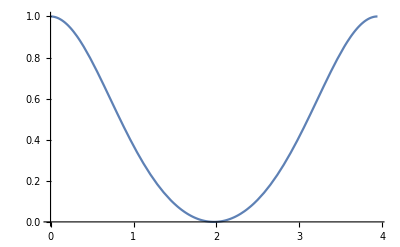

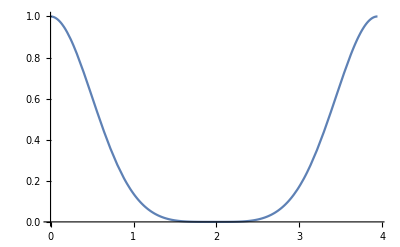

```mathematica
Plot[JacobiCN[x,mmm]^2,{x,0,Period/4}]
Plot[JacobiCN[x,mmm]^4,{x,0,Period/4}]
```

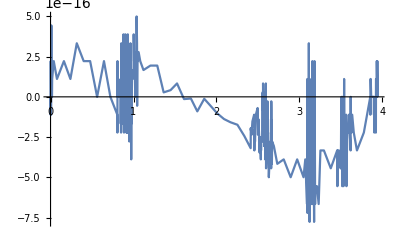

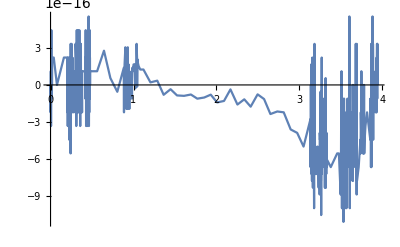

```mathematica
Plot[JacobiCN[x,mmm]^2-FS2,{x,0,Period/4}]
Plot[JacobiCN[x,mmm]^4-FS4,{x,0,Period/4}]
```

```mathematica
D0 = IdentityMatrix[2*nmodes+1];
D1 = DiagonalMatrix[Table[I σ k Pi/KI,{k,-nmodes,nmodes}] ];
D2=D1.D1;
D3=D2.D1;
D4=D2.D2;
D5 = D2.D3;
FC = Join[{B1 + B2 A02 + B3 A04}, Table[B2 AF2[k] + B3 AF4[k],{k,1,2*nmodes}]];
QM = ToeplitzMatrix[FC];
```

```mathematica
LinOp[μ_]:= -(D5- 5 I μ D4 - 10 μ^2 D3 + 10 I μ^3 D2 + 5 μ^4 D1 - I μ^5 IdentityMatrix[2*nmodes+1]) + α(D3 - 3 I μ D2 - 3 μ^2 D1 + I μ^3 D0)+(D1-I μ D0).QM
```

Compute the spectrum for μ=0. The kernel there should be of higher multiplicity.  In this case it appears to have spectral multiplicity three.

```mathematica
Chop[Eigenvalues[LinOp[0.0]],10^(-5)]
```

{0.+31218.9 ⅈ,0.-31218.9 ⅈ,0.-24073.1 ⅈ,0.+24073.1 ⅈ,0.+18296.2 ⅈ,0.-18296.2 ⅈ,0.+13682.1 ⅈ,0.-13682.1 ⅈ,0.-10046.2 ⅈ,0.+10046.2 ⅈ,0.+7224.86 ⅈ,0.-7224.86 ⅈ,0.+5073.33 ⅈ,0.-5073.33 ⅈ,0.+3465.25 ⅈ,0.-3465.25 ⅈ,0.-2291.09 ⅈ,0.+2291.09 ⅈ,0.+1457.04 ⅈ,0.-1457.04 ⅈ,0.-883.824 ⅈ,0.+883.824 ⅈ,0.-505.419 ⅈ,0.+505.419 ⅈ,0.-267.905 ⅈ,0.+267.905 ⅈ,0.-128.236 ⅈ,0.+128.236 ⅈ,0.-53.0343 ⅈ,0.+53.0343 ⅈ,0.-17.3798 ⅈ,0.+17.3798 ⅈ,0.+3.60688 ⅈ,0.-3.60688 ⅈ,0.-0.278052 ⅈ,0.+0.278052 ⅈ,0.+0.0221817 ⅈ,0.-0.0221817 ⅈ,0,0,0}

Compute the spectrum of the linearized operator by computing the eigenvalues for each value of μ, the Floquet exponent, for a large collection of μ.

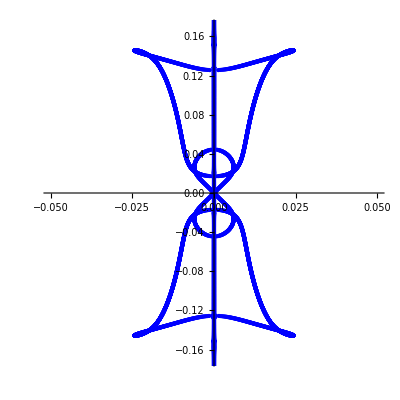

```mathematica
Evals = Flatten[Table[Eigenvalues[LinOp[x]],{x,-σ Pi/(2KI),σ Pi/(2KI),0.0002 }]];
KawaharaSpectrum=ComplexListPlot[Evals,PlotRange->{{-.05,.05},{-0.17,0.17}},PlotStyle->{Blue,PointSize[Small]},AspectRatio->1]
```

.

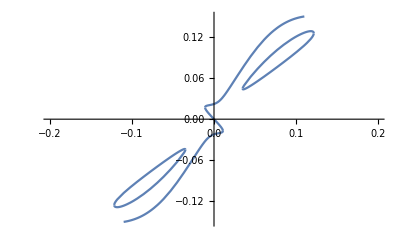

```mathematica
AllEig[fe_,num_] := Take[Sort[Chop[-I Eigenvalues[LinOp[fe]]]],num]
AllEig2[fe_,num_] := Take[Sort[Re[Chop[Eigenvalues[LinOp[fe]]]]],num]
BandsPlot=Plot[AllEig[fee,41],{fee,-σ Pi/(2KI),σ Pi/(2KI)},PlotRange->{{-σ Pi/(2KI),σ Pi/(2KI)},{-.15,.15}}]
```

```mathematica
KSolve[λ_?NumericQ]:=NDSolve[{u1'[xx]==v1[xx],v1'[xx]==w1[xx],w1'[xx]==y1[xx],y1'[xx]==z1[xx],z1'[xx]== λ u1[xx]+ ϕ[xx] v1[xx] + α y1[xx],u2'[xx]==v2[xx],v2'[xx]==w2[xx],w2'[xx]==y2[xx],y2'[xx]==z2[xx],z2'[xx]==λ u2[xx] + ϕ[xx] v2[xx] + α y2[xx],u3'[xx]==v3[xx],v3'[xx]==w3[xx],w3'[xx]==y3[xx],y3'[xx]==z3[xx],z3'[xx] ==λ u3[xx]+ ϕ[xx] v3[xx] + α y3[xx],u4'[xx]==v4[xx],v4'[xx]==w4[xx],w4'[xx]==y4[xx],y4'[xx]==z4[xx],z4'[xx] ==λ u4[xx]+ ϕ[xx] v4[xx]  + α y4[xx],u5'[xx]==v5[xx],v5'[xx]==w5[xx],w5'[xx]==y5[xx],y5'[xx]==z5[xx],z5'[xx]==λ u5[xx]+ ϕ[xx] v5[xx]  + α y5[xx],du1'[xx]==dv1[xx],dv1'[xx]==dw1[xx],dw1'[xx]==dy1[xx],dy1'[xx]==dz1[xx],dz1'[xx]== λ du1[xx]+ u1[xx]+ϕ[xx] dv1[xx]  + α dy1[xx],du2'[xx]==dv2[xx],dv2'[xx]==dw2[xx],dw2'[xx]==dy2[xx],dy2'[xx]==dz2[xx],dz2'[xx]==λ du2[xx] + u2[xx]+ ϕ[xx] dv2[xx]  + α dy2[xx],du3'[xx]==dv3[xx],dv3'[xx]==dw3[xx],dw3'[xx]==dy3[xx],dy3'[xx]==dz3[xx],dz3'[xx] ==λ du3[xx]+ u3[xx]+ ϕ[xx] dv3[xx] + α dy3[xx],du4'[xx]==dv4[xx],dv4'[xx]==dw4[xx],dw4'[xx]==dy4[xx],dy4'[xx]==dz4[xx],dz4'[xx] ==λ du4[xx]+ u4[xx]+ ϕ[xx] dv4[xx] + α dy4[xx],du5'[xx]==dv5[xx],dv5'[xx]==dw5[xx],dw5'[xx]==dy5[xx],dy5'[xx]==dz5[xx],dz5'[xx]==λ du5[xx]+ u5[xx]+ ϕ[xx] dv5[xx]  + α dy5[xx],u1[0]==1,v1[0]==0,w1[0]==0,y1[0]==0,z1[0]==0,u2[0]==0,v2[0]==1,w2[0]==0,y2[0]==0,z2[0]==0,u3[0]==0,v3[0]==0,w3[0]==1,y3[0]==0,z3[0]==0,u4[0]==0,v4[0]==0,w4[0]==0,y4[0]==1,z4[0]==0,u5[0]==0,v5[0]==0,w5[0]==0,y5[0]==0,z5[0]==1,du1[0]==0,dv1[0]==0,dw1[0]==0,dy1[0]==0,dz1[0]==0,du2[0]==0,dv2[0]==0,dw2[0]==0,dy2[0]==0,dz2[0]==0,du3[0]==0,dv3[0]==0,dw3[0]==0,dy3[0]==0,dz3[0]==0,du4[0]==0,dv4[0]==0,dw4[0]==0,dy4[0]==0,dz4[0]==0,du5[0]==0,dv5[0]==0,dw5[0]==0,dy5[0]==0,dz5[0]==0},{u1,v1,w1,y1,z1,u2,v2,w2,y2,z2,u3,v3,w3,y3,z3,u4,v4,w4,y4,z4,u5,v5,w5,y5,z5,du1,dv1,dw1,dy1,dz1,du2,dv2,dw2,dy2,dz2,du3,dv3,dw3,dy3,dz3,du4,dv4,dw4,dy4,dz4,du5,dv5,dw5,dy5,dz5},{xx,0,2 Period}]
```

Next compute the monodromy matrix and the associated invariants and their derivatives .

```mathematica
mon[l_] := Evaluate[{{u1[Period],u2[Period],u3[Period],u4[Period],u5[Period]},{v1[Period],v2[Period],v3[Period],v4[Period],v5[Period]},{w1[Period],w2[Period],w3[Period],w4[Period],w5[Period]},{y1[Period],y2[Period],y3[Period],y4[Period],y5[Period]},{z1[Period],z2[Period],z3[Period],z4[Period],z5[Period]}}]/. KSolve[l][[1]]
CharPoly[l_] := CharacteristicPolynomial[mon[l],x]
f[l_] := (u1[Period] + v2[Period]+w3[Period]+y4[Period]+z5[Period]) /. KSolve[l][[1]]
g[l_]:= (-v1[Period] u2[Period]-w1[Period] u3[Period]-w2[Period] v3[Period]+v2[Period] w3[Period]-y1[Period] u4[Period]-y2[Period] v4[Period]-y3[Period] w4[Period]+v2[Period] y4[Period]+w3[Period] y4[Period]-z1[Period] u5[Period]-z2[Period] v5[Period]-z3[Period] w5[Period]-z4[Period] y5[Period]+v2[Period] z5[Period]+w3[Period] z5[Period]+y4[Period] z5[Period]+u1[Period] (v2[Period]+w3[Period]+y4[Period]+z5[Period])) /. KSolve[l][[1]]
df[l_] := (du1[Period] + dv2[Period]+dw3[Period]+dy4[Period]+dz5[Period]) /. KSolve[l][[1]]
dg[l_] := -Tr[{{u1[Period],u2[Period],u3[Period],u4[Period],u5[Period]},{v1[Period],v2[Period],v3[Period],v4[Period],v5[Period]},{w1[Period],w2[Period],w3[Period],w4[Period],w5[Period]},{y1[Period],y2[Period],y3[Period],y4[Period],y5[Period]},{z1[Period],z2[Period],z3[Period],z4[Period],z5[Period]}}.{{du1[Period],du2[Period],du3[Period],du4[Period],du5[Period]},{dv1[Period],dv2[Period],dv3[Period],dv4[Period],dv5[Period]},{dw1[Period],dw2[Period],dw3[Period],dw4[Period],dw5[Period]},{dy1[Period],dy2[Period],dy3[Period],dy4[Period],dy5[Period]},{dz1[Period],dz2[Period],dz3[Period],dz4[Period],dz5[Period]}}]+ (u1[Period] + v2[Period]+w3[Period]+y4[Period]+z5[Period])(du1[Period] + dv2[Period]+dw3[Period]+dy4[Period]+dz5[Period])/. KSolve[l][[1]]
Invar2RI[l_] := {Re[(u1[Period] + v2[Period]+w3[Period]+y4[Period]+z5[Period])],Im[(u1[Period] + v2[Period]+w3[Period]+y4[Period]+z5[Period])],Re[(-v1[Period] u2[Period]-w1[Period] u3[Period]-w2[Period] v3[Period]+v2[Period] w3[Period]-y1[Period] u4[Period]-y2[Period] v4[Period]-y3[Period] w4[Period]+v2[Period] y4[Period]+w3[Period] y4[Period]-z1[Period] u5[Period]-z2[Period] v5[Period]-z3[Period] w5[Period]-z4[Period] y5[Period]+v2[Period] z5[Period]+w3[Period] z5[Period]+y4[Period] z5[Period]+u1[Period] (v2[Period]+w3[Period]+y4[Period]+z5[Period]))],Im[(-v1[Period] u2[Period]-w1[Period] u3[Period]-w2[Period] v3[Period]+v2[Period] w3[Period]-y1[Period] u4[Period]-y2[Period] v4[Period]-y3[Period] w4[Period]+v2[Period] y4[Period]+w3[Period] y4[Period]-z1[Period] u5[Period]-z2[Period] v5[Period]-z3[Period] w5[Period]-z4[Period] y5[Period]+v2[Period] z5[Period]+w3[Period] z5[Period]+y4[Period] z5[Period]+u1[Period] (v2[Period]+w3[Period]+y4[Period]+z5[Period]))]}/. KSolve[l][[1]]
Invar4[l_]:= {(u1[Period] + v2[Period]+w3[Period]+y4[Period]+z5[Period]),(-v1[Period] u2[Period]-w1[Period] u3[Period]-w2[Period] v3[Period]+v2[Period] w3[Period]-y1[Period] u4[Period]-y2[Period] v4[Period]-y3[Period] w4[Period]+v2[Period] y4[Period]+w3[Period] y4[Period]-z1[Period] u5[Period]-z2[Period] v5[Period]-z3[Period] w5[Period]-z4[Period] y5[Period]+v2[Period] z5[Period]+w3[Period] z5[Period]+y4[Period] z5[Period]+u1[Period] (v2[Period]+w3[Period]+y4[Period]+z5[Period])),(du1[Period] + dv2[Period]+dw3[Period]+dy4[Period]+dz5[Period]),-Tr[{{u1[Period],u2[Period],u3[Period],u4[Period],u5[Period]},{v1[Period],v2[Period],v3[Period],v4[Period],v5[Period]},{w1[Period],w2[Period],w3[Period],w4[Period],w5[Period]},{y1[Period],y2[Period],y3[Period],y4[Period],y5[Period]},{z1[Period],z2[Period],z3[Period],z4[Period],z5[Period]}}.{{du1[Period],du2[Period],du3[Period],du4[Period],du5[Period]},{dv1[Period],dv2[Period],dv3[Period],dv4[Period],dv5[Period]},{dw1[Period],dw2[Period],dw3[Period],dw4[Period],dw5[Period]},{dy1[Period],dy2[Period],dy3[Period],dy4[Period],dy5[Period]},{dz1[Period],dz2[Period],dz3[Period],dz4[Period],dz5[Period]}}]+ (u1[Period] + v2[Period]+w3[Period]+y4[Period]+z5[Period])(du1[Period] + dv2[Period]+dw3[Period]+dy4[Period]+dz5[Period])} /. KSolve[l][[1]]
CP2[l_] := -x^5 + f[l] x^4 - g[l] x^3 + Conjugate[g[l]] x^2 - Conjugate[f[l]]x + 1
dCP2[l_] := df[l] x^4 - dg[l] x^3 - dg[-l] x^2 + df[-l] x
```

Check that the characteristic polynomial has the appropriate symmetry and that the derivatives agree with the results of numerical differentiation

```mathematica
CharPoly[3.0I]
Timing[Invar4[3.0I]]
f[3.0I]
g[3.0I]
df[3.0I]
(f[3.0001I]-f[2.9999I])/(.0002I)
dg[3.0I]
(g[3.0001I]-g[2.9999I])/(.0002I)
```

(0.999958-0.0000586691 ⅈ)-(120968.-951384. ⅈ) x+(5.45656×10^9-1.59364×10^9 ⅈ) x^2-(5.45658×10^9+1.5936×10^9 ⅈ) x^3+(120972.+951387. ⅈ) x^4-x^5

{0.03335,{120972.+951387. ⅈ,5.45658×10^9+1.5936×10^9 ⅈ,1.54258×10^6+82567. ⅈ,1.30687×10^9-1.46008×10^10 ⅈ}}

120972.+951387. ⅈ

5.45658×10^9+1.5936×10^9 ⅈ

1.54258×10^6+82567. ⅈ

1.54258×10^6+82581.7 ⅈ

1.30687×10^9-1.46008×10^10 ⅈ

1.3072×10^9-1.46007×10^10 ⅈ

```mathematica
CharPoly[0.18I]
```

(0.999998-5.59188×10^-8 ⅈ)+(5.33562+4.30217 ⅈ) x+(3.04078+16.2572 ⅈ) x^2-(3.04085-16.2572 ⅈ) x^3-(5.33564-4.30216 ⅈ) x^4-x^5

```mathematica
Solve[%==0,x]
```

{{x→-3.55716+1.55228 ⅈ},{x→-0.91429-0.40506 ⅈ},{x→-0.554806+2.69604 ⅈ},{x→-0.236152+0.103053 ⅈ},{x→-0.073227+0.355845 ⅈ}}

```mathematica
Abs[x /. %1361]
```

{3.88111,1.,2.75253,0.257658,0.363301}

```mathematica
CPSymb = 1-fc[λ] x+gc[λ] x^2-g1[λ] x^3+f1[λ] x^4-x^5;
Resultant[CPSymb,D[CPSymb,λ],x] /. {f1[λ]-> I1, g1[λ]->I2 , fc[λ]-> Conjugate[I1], gc[λ]->Conjugate[I2], f1'[λ]->I3, g1'[λ]->I4,fc'[λ]->-Conjugate[I3], gc'[λ]->-Conjugate[I4]};
Disco[{a_,b_,c_,d_}] := -(-3125+2500 a^2+50 a^4-512 a^5+36 a^6+27 a^8+2500 b^2+100 a^2 b^2+5120 a^3 b^2+108 a^4 b^2+108 a^6 b^2+50 b^4-2560 a b^4+108 a^2 b^4+162 a^4 b^4+36 b^6+108 a^2 b^6+27 b^8-4000 a^2 c+3200 a^3 c-320 a^4 c+384 a^5 c-288 a^6 c+4000 b^2 c-9600 a b^2 c-768 a^3 b^2 c-288 a^4 b^2 c+320 b^4 c-1152 a b^4 c+288 a^2 b^4 c+288 b^6 c+3750 c^2-4500 a c^2+2050 a^2 c^2-2040 a^3 c^2+1002 a^4 c^2+12 a^5 c^2-18 a^6 c^2+2050 b^2 c^2-2040 a b^2 c^2-44 a^2 b^2 c^2+24 a^3 b^2 c^2-54 a^4 b^2 c^2+1002 b^4 c^2+12 a b^4 c^2-54 a^2 b^4 c^2-18 b^6 c^2+1800 a c^3-1120 a^2 c^3-336 a^3 c^3+160 a^4 c^3+8 a^5 c^3+1120 b^2 c^3+816 a b^2 c^3+16 a^3 b^2 c^3-160 b^4 c^3+8 a b^4 c^3-825 c^4+1260 a c^4-302 a^2 c^4-68 a^3 c^4-a^4 c^4-410 b^2 c^4+60 a b^2 c^4-2 a^2 b^2 c^4-b^4 c^4-216 c^5+144 a c^5+8 a^2 c^5-8 b^2 c^5-16 c^6-8000 a b d-9600 a^2 b d-640 a^3 b d-1152 a^4 b d-576 a^5 b d+3200 b^3 d-640 a b^3 d-768 a^2 b^3 d-1152 a^3 b^3 d+384 b^5 d-576 a b^5 d+9000 b c d+4080 a^2 b c d+2048 a^3 b c d-24 a^4 b c d+4080 b^3 c d-2048 a b^3 c d-48 a^2 b^3 c d-24 b^5 c d+5400 b c^2 d-2240 a b c^2 d+720 a^2 b c^2 d+320 a^3 b c^2 d+24 a^4 b c^2 d-432 b^3 c^2 d+320 a b^3 c^2 d+48 a^2 b^3 c^2 d+24 b^5 c^2 d-2520 b c^3 d-432 a b c^3 d-312 a^2 b c^3 d+200 b^3 c^3 d+432 b c^4 d+16 a b c^4 d+3750 d^2+4500 a d^2+2050 a^2 d^2+2040 a^3 d^2+490 a^4 d^2-12 a^5 d^2-18 a^6 d^2+2050 b^2 d^2+2040 a b^2 d^2+3028 a^2 b^2 d^2-24 a^3 b^2 d^2-54 a^4 b^2 d^2+490 b^4 d^2-12 a b^4 d^2-54 a^2 b^4 d^2-18 b^6 d^2-5400 a c d^2-1120 a^2 c d^2-144 a^3 c d^2+160 a^4 c d^2-24 a^5 c d^2+1120 b^2 c d^2+1008 a b^2 c d^2-48 a^3 b^2 c d^2-160 b^4 c d^2-24 a b^4 c d^2-1650 c^2 d^2-1036 a^2 c^2 d^2+192 a^3 c^2 d^2-2 a^4 c^2 d^2-388 b^2 c^2 d^2-576 a b^2 c^2 d^2-4 a^2 b^2 c^2 d^2-2 b^4 c^2 d^2+2160 c^3 d^2-288 a c^3 d^2+16 a^2 c^3 d^2-16 b^2 c^3 d^2-48 c^4 d^2-1800 b d^3-2240 a b d^3+912 a^2 b d^3+320 a^3 b d^3-8 a^4 b d^3-240 b^3 d^3+320 a b^3 d^3-16 a^2 b^3 d^3-8 b^5 d^3-2520 b c d^3+432 a b c d^3+456 a^2 b c d^3-56 b^3 c d^3+288 b c^2 d^3+32 a b c^2 d^3-825 d^4-1260 a d^4-302 a^2 d^4+4 a^3 d^4-a^4 d^4-410 b^2 d^4+132 a b^2 d^4-2 a^2 b^2 d^4-b^4 d^4-1080 c d^4-432 a c d^4+8 a^2 c d^4-8 b^2 c d^4-48 c^2 d^4-144 b d^5+16 a b d^5-16 d^6)
BifIndex[{I1_,I2_,I3_,I4_}]:= I3^5-I2 I3^2 I4^3+I1 I3 I4^4-I4^5-I3^4 I4 Conjugate[I1]+I3^3 I4^2 Conjugate[I2]+3 I2 I3^4 Conjugate[I3]-4 I1 I3^3 I4 Conjugate[I3]+5 I3^2 I4^2 Conjugate[I3]+I2 I3^3 I4 Conjugate[I1] Conjugate[I3]-I1 I3^2 I4^2 Conjugate[I1] Conjugate[I3]+I3 I4^3 Conjugate[I1] Conjugate[I3]+I2 I3^2 I4^2 Conjugate[I1]^2 Conjugate[I3]-I1 I3 I4^3 Conjugate[I1]^2 Conjugate[I3]+I4^4 Conjugate[I1]^2 Conjugate[I3]+I3^4 Conjugate[I1]^3 Conjugate[I3]-2 I2 I3^2 I4^2 Conjugate[I2] Conjugate[I3]+2 I1 I3 I4^3 Conjugate[I2] Conjugate[I3]-2 I4^4 Conjugate[I2] Conjugate[I3]-3 I3^4 Conjugate[I1] Conjugate[I2] Conjugate[I3]-I3^3 I4 Conjugate[I1]^2 Conjugate[I2] Conjugate[I3]+2 I3^3 I4 Conjugate[I2]^2 Conjugate[I3]+3 I2^2 I3^3 Conjugate[I3]^2-5 I1 I2 I3^2 I4 Conjugate[I3]^2+2 I1^2 I3 I4^2 Conjugate[I3]^2+3 I2 I3 I4^2 Conjugate[I3]^2-2 I1 I4^3 Conjugate[I3]^2-3 I3^3 Conjugate[I1] Conjugate[I3]^2+2 I2^2 I3^2 I4 Conjugate[I1] Conjugate[I3]^2-2 I1 I2 I3 I4^2 Conjugate[I1] Conjugate[I3]^2+2 I2 I4^3 Conjugate[I1] Conjugate[I3]^2+3 I1 I3^3 Conjugate[I1]^2 Conjugate[I3]^2-4 I3^2 I4 Conjugate[I1]^2 Conjugate[I3]^2-3 I1 I3^3 Conjugate[I2] Conjugate[I3]^2+7 I3^2 I4 Conjugate[I2] Conjugate[I3]^2-3 I2 I3^3 Conjugate[I1] Conjugate[I2] Conjugate[I3]^2+I1 I3^2 I4 Conjugate[I1] Conjugate[I2] Conjugate[I3]^2-I3 I4^2 Conjugate[I1] Conjugate[I2] Conjugate[I3]^2-I2 I3^2 I4 Conjugate[I2]^2 Conjugate[I3]^2+I1 I3 I4^2 Conjugate[I2]^2 Conjugate[I3]^2-I4^3 Conjugate[I2]^2 Conjugate[I3]^2+I3^3 Conjugate[I2]^3 Conjugate[I3]^2-3 I1 I3^2 Conjugate[I3]^3+I2^3 I3^2 Conjugate[I3]^3+5 I3 I4 Conjugate[I3]^3-I1 I2^2 I3 I4 Conjugate[I3]^3+I2^2 I4^2 Conjugate[I3]^3+3 I1^2 I3^2 Conjugate[I1] Conjugate[I3]^3-3 I2 I3^2 Conjugate[I1] Conjugate[I3]^3-5 I1 I3 I4 Conjugate[I1] Conjugate[I3]^3+2 I4^2 Conjugate[I1] Conjugate[I3]^3-3 I1 I2 I3^2 Conjugate[I2] Conjugate[I3]^3+2 I1^2 I3 I4 Conjugate[I2] Conjugate[I3]^3+I2 I3 I4 Conjugate[I2] Conjugate[I3]^3-2 I1 I4^2 Conjugate[I2] Conjugate[I3]^3+3 I3^2 Conjugate[I2]^2 Conjugate[I3]^3+I1^3 I3 Conjugate[I3]^4-3 I1 I2 I3 Conjugate[I3]^4-I1^2 I4 Conjugate[I3]^4+2 I2 I4 Conjugate[I3]^4+3 I3 Conjugate[I2] Conjugate[I3]^4+Conjugate[I3]^5-3 I2 I3^3 I4 Conjugate[I4]+4 I1 I3^2 I4^2 Conjugate[I4]-5 I3 I4^3 Conjugate[I4]-I2 I3^2 I4^2 Conjugate[I1] Conjugate[I4]+I1 I3 I4^3 Conjugate[I1] Conjugate[I4]-I4^4 Conjugate[I1] Conjugate[I4]-I3^4 Conjugate[I1]^2 Conjugate[I4]+2 I3^4 Conjugate[I2] Conjugate[I4]+I3^3 I4 Conjugate[I1] Conjugate[I2] Conjugate[I4]+5 I3^3 Conjugate[I3] Conjugate[I4]-3 I2^2 I3^2 I4 Conjugate[I3] Conjugate[I4]+3 I1 I2 I3 I4^2 Conjugate[I3] Conjugate[I4]-3 I2 I4^3 Conjugate[I3] Conjugate[I4]-5 I1 I3^3 Conjugate[I1] Conjugate[I3] Conjugate[I4]+7 I3^2 I4 Conjugate[I1] Conjugate[I3] Conjugate[I4]+2 I2 I3^3 Conjugate[I1]^2 Conjugate[I3] Conjugate[I4]-3 I1 I3^2 I4 Conjugate[I1]^2 Conjugate[I3] Conjugate[I4]+4 I3 I4^2 Conjugate[I1]^2 Conjugate[I3] Conjugate[I4]+I2 I3^3 Conjugate[I2] Conjugate[I3] Conjugate[I4]+4 I1 I3^2 I4 Conjugate[I2] Conjugate[I3] Conjugate[I4]-6 I3 I4^2 Conjugate[I2] Conjugate[I3] Conjugate[I4]+I2 I3^2 I4 Conjugate[I1] Conjugate[I2] Conjugate[I3] Conjugate[I4]-I1 I3 I4^2 Conjugate[I1] Conjugate[I2] Conjugate[I3] Conjugate[I4]+I4^3 Conjugate[I1] Conjugate[I2] Conjugate[I3] Conjugate[I4]-I3^3 Conjugate[I1] Conjugate[I2]^2 Conjugate[I3] Conjugate[I4]-4 I1^2 I3^2 Conjugate[I3]^2 Conjugate[I4]+7 I2 I3^2 Conjugate[I3]^2 Conjugate[I4]+7 I1 I3 I4 Conjugate[I3]^2 Conjugate[I4]-5 I4^2 Conjugate[I3]^2 Conjugate[I4]+I1 I2 I3^2 Conjugate[I1] Conjugate[I3]^2 Conjugate[I4]-3 I1^2 I3 I4 Conjugate[I1] Conjugate[I3]^2 Conjugate[I4]+4 I2 I3 I4 Conjugate[I1] Conjugate[I3]^2 Conjugate[I4]+3 I1 I4^2 Conjugate[I1] Conjugate[I3]^2 Conjugate[I4]-I2^2 I3^2 Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]+I1 I2 I3 I4 Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]-I2 I4^2 Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]-5 I3^2 Conjugate[I1] Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]+2 I1 I3^2 Conjugate[I2]^2 Conjugate[I3]^2 Conjugate[I4]-3 I3 I4 Conjugate[I2]^2 Conjugate[I3]^2 Conjugate[I4]-I1^2 I2 I3 Conjugate[I3]^3 Conjugate[I4]+2 I2^2 I3 Conjugate[I3]^3 Conjugate[I4]+I1 I2 I4 Conjugate[I3]^3 Conjugate[I4]-4 I3 Conjugate[I1] Conjugate[I3]^3 Conjugate[I4]+I1 I3 Conjugate[I2] Conjugate[I3]^3 Conjugate[I4]-3 I4 Conjugate[I2] Conjugate[I3]^3 Conjugate[I4]-I1 Conjugate[I3]^4 Conjugate[I4]+2 I1 I3^3 Conjugate[I4]^2-5 I3^2 I4 Conjugate[I4]^2-2 I2 I3^3 Conjugate[I1] Conjugate[I4]^2+3 I1 I3^2 I4 Conjugate[I1] Conjugate[I4]^2-4 I3 I4^2 Conjugate[I1] Conjugate[I4]^2-I2 I3^2 I4 Conjugate[I2] Conjugate[I4]^2+I1 I3 I4^2 Conjugate[I2] Conjugate[I4]^2-I4^3 Conjugate[I2] Conjugate[I4]^2+I3^3 Conjugate[I2]^2 Conjugate[I4]^2-I1 I2 I3^2 Conjugate[I3] Conjugate[I4]^2+4 I1^2 I3 I4 Conjugate[I3] Conjugate[I4]^2-6 I2 I3 I4 Conjugate[I3] Conjugate[I4]^2-4 I1 I4^2 Conjugate[I3] Conjugate[I4]^2+I2^2 I3^2 Conjugate[I1] Conjugate[I3] Conjugate[I4]^2-I1 I2 I3 I4 Conjugate[I1] Conjugate[I3] Conjugate[I4]^2+I2 I4^2 Conjugate[I1] Conjugate[I3] Conjugate[I4]^2+2 I3^2 Conjugate[I1]^2 Conjugate[I3] Conjugate[I4]^2+3 I3^2 Conjugate[I2] Conjugate[I3] Conjugate[I4]^2-2 I1 I3^2 Conjugate[I1] Conjugate[I2] Conjugate[I3] Conjugate[I4]^2+3 I3 I4 Conjugate[I1] Conjugate[I2] Conjugate[I3] Conjugate[I4]^2+5 I3 Conjugate[I3]^2 Conjugate[I4]^2-I1 I3 Conjugate[I1] Conjugate[I3]^2 Conjugate[I4]^2+4 I4 Conjugate[I1] Conjugate[I3]^2 Conjugate[I4]^2+I1^2 I3 Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]^2-2 I2 I3 Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]^2-I1 I4 Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]^2+I2 Conjugate[I3]^3 Conjugate[I4]^2-I2^2 I3^2 Conjugate[I4]^3+I1 I2 I3 I4 Conjugate[I4]^3-I2 I4^2 Conjugate[I4]^3-2 I3^2 Conjugate[I1] Conjugate[I4]^3+2 I1 I3^2 Conjugate[I2] Conjugate[I4]^3-3 I3 I4 Conjugate[I2] Conjugate[I4]^3+I1 I3 Conjugate[I3] Conjugate[I4]^3-5 I4 Conjugate[I3] Conjugate[I4]^3-I1^2 I3 Conjugate[I1] Conjugate[I3] Conjugate[I4]^3+2 I2 I3 Conjugate[I1] Conjugate[I3] Conjugate[I4]^3+I1 I4 Conjugate[I1] Conjugate[I3] Conjugate[I4]^3-Conjugate[I2] Conjugate[I3]^2 Conjugate[I4]^3+I1^2 I3 Conjugate[I4]^4-2 I2 I3 Conjugate[I4]^4-I1 I4 Conjugate[I4]^4+Conjugate[I1] Conjugate[I3] Conjugate[I4]^4-Conjugate[I4]^5
Disco2[l_] := Disco[Invar2RI[l]]
```

```mathematica
``
```

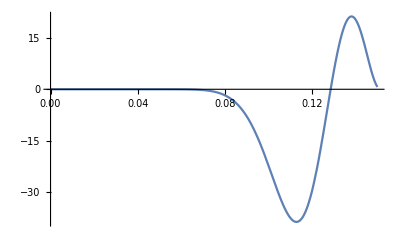

```mathematica
Plot[Re[Disco2[I x]],{x,0,0.15}]
```

-Graphics-

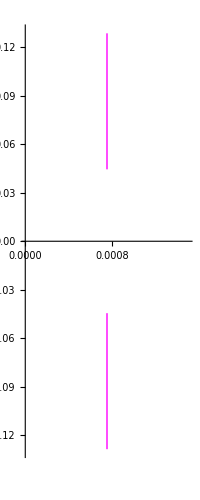

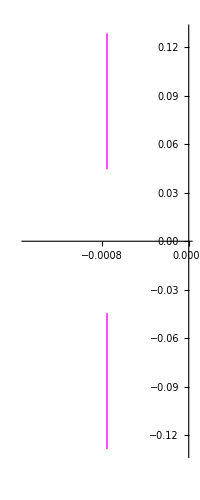

```mathematica
BifIndPlot=ParametricPlot[{Re[BifIndex[Invar4[x I]]],x},{x,-0.25,0.25},PlotStyle->{Red,Thick,Dashed}]
Side[l_] := If[Re[Disco2[l]]<-10^(-5),.005,I]
S1=ParametricPlot[{.15*Side[I x],x},{x,-.2,.2},PlotStyle->{Thick,Magenta}]
S2=ParametricPlot[{-.15*Side[I x],x},{x,-.2,.2},PlotStyle->{Thick,Magenta}]
```

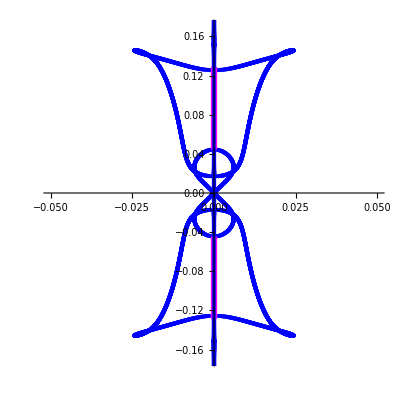

```mathematica
UnstableKawaharaFigure1=Show[KawaharaSpectrum,BifIndPlot,S1,S2]
```

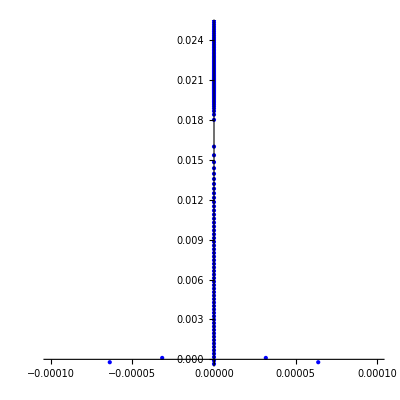

```mathematica
UnstableKawaharaFigure1Zoom= Show[KawaharaSpectrum,BifIndPlot,PlotRange->{{-.0001,.0001},{0,.025}}]
```

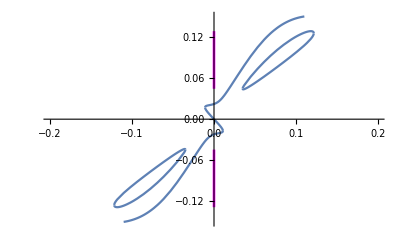

```mathematica
UnstableKawaharBandPlot=Show[BandsPlot,S1,S2]
```

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1.pdf",UnstableKawaharaFigure1]
```

~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1.pdf

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1.png",UnstableKawaharaFigure1]
```

~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1.png

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1Zoom.pdf",UnstableKawaharaFigure1Zoom]
```

~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1Zoom.pdf

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1Zoom.png",UnstableKawaharaFigure1Zoom]
```

~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharaFigure1Zoom.png

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharBandPlot.pdf",UnstableKawaharBandPlot]
```

~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharBandPlot.pdf

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharBandPlot.png",UnstableKawaharBandPlot]
```

~/Dropbox/Jared Robby/Schmoopys/Kawahara/UnstableKawaharBandPlot.png